# Regular Black Hole

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

## Der Ricci-Skalar

```mathematica
ClearAll[R];
R00 = 1/2 V''[r] - (n+2)/2 V'[r]/r; Rii =(1+n) V[r]/r^2+V'[r]/r;
R[r_,V_] = 2 R00 + (n+2) Rii // FullSimplify
```

((1+n) (2+n) V[r])/r^2+V''[r]

Da ist er schon! Nun setzen wir für V(r) etwas ein.

```mathematica
ClearAll[V]
V[r_,H_] = 2/(n+2)M/Mstar H[r]/r^(n+1)
```

(2 M r^(-1-n) H[r])/(Mstar (2+n))

```mathematica
Vh[H_] = V[#,H]&; (* Gibt ein V[r] fuer H aus. *)
R[r,Vh@H] // FullSimplify
```

(r^(-3-n) (4 M (1+n) ((2+n) H[r]-r H'[r])+2 M r^2 H''[r]))/(Mstar (2+n))

```mathematica
holo[r_] =r^(2+n)/(r^(2+n) + 1);
halpha[r_] =r^(3+n)/((r^α+L^α/2)^((3+n)/α));
α0[n_] = (3+n)/Log[2+n] Log[(3+n)/2];
```

```mathematica
holoR[r_] = R[r, Vh@holo] /. {Mstar -> 1, M-> 1, n-> 0}
```

4/(r (1+r^2))+((8 r^4)/((1+r^2)^3)-(10 r^2)/((1+r^2)^2)+2/(1+r^2))/r-(2 (-(2 r^3)/((1+r^2)^2)+(2 r)/(1+r^2)))/r^2

```mathematica
halphaR[r_] = R[r,Vh@halpha] //. {Mstar -> 1, M-> 1,n-> 0, α-> α0[n],L-> 1}
```

4 (1/2+r^((3 Log[3/2])/Log[2]))^(-Log[2]/Log[3/2])-(2 (3 r^2 (1/2+r^((3 Log[3/2])/Log[2]))^(-Log[2]/Log[3/2])-3 r^(2+(3 Log[3/2])/Log[2]) (1/2+r^((3 Log[3/2])/Log[2]))^(-1-Log[2]/Log[3/2])))/r^2+1/r(6 r (1/2+r^((3 Log[3/2])/Log[2]))^(-Log[2]/Log[3/2])-9 r^(1+(3 Log[3/2])/Log[2]) (1/2+r^((3 Log[3/2])/Log[2]))^(-1-Log[2]/Log[3/2])-3 r^(1+(3 Log[3/2])/Log[2]) (1/2+r^((3 Log[3/2])/Log[2]))^(-1-Log[2]/Log[3/2]) (2+(3 Log[3/2])/Log[2])-(9 r^(1+(6 Log[3/2])/Log[2]) (1/2+r^((3 Log[3/2])/Log[2]))^(-2-Log[2]/Log[3/2]) Log[3/2] (-1-Log[2]/Log[3/2]))/Log[2])

```mathematica
halphaInfR[r_] = R[r,Vh@halpha] //. {Mstar -> 1, M-> 1,n-> 0, α->100000,L-> 1};
```

```mathematica
(* Nur so im Vergleich, sieht im Plot nicht besonders gut aus *)
SchwarzschildR[r_] =R[r,Function[r,2/(n+2)1/r^(1+n)]]/. n-> 0 // Expand
```

4/r^3

```mathematica
deSitterR[r_] = R[r,Function[r,2 r^2]] /. n-> 0 // Expand
```

8

## Limites und Plot

```mathematica
Limit[holoR[r],r-> 0]
```

∞

```mathematica
Limit[halphaR[r],r-> 0] // N
```

13.082

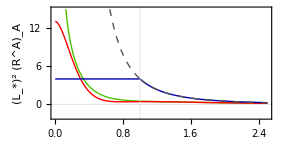

```mathematica
fig=Plot[Evaluate@{holoR[r],halphaR[r],halphaInfR[r],SchwarzschildR[r]},{r,0,2.5},PlotRange-> {-2,15},
Frame-> True,
GridLines-> {{1},{0}},
FrameLabel-> {"r/L_*", "(L_*)^2 (R^A)_A"},
PlotStyle-> {Blend[{Darker@Green,Yellow},0.3], {Red},{Thick,Darker@Blue},{Dashed,Darker@Gray}},
ImageSize -> 10cm,
Exclusions-> {1.0},
PlotRangePadding->None,
AspectRatio-> 0.50,
PlotLegends->Placed[{"Holographic","self-regular α=α_0","self-regular α=∞","Schwarzschild"},{Right,Top}]
]
```

```mathematica
Export["../figures/ricci-scalar.pdf", Show@fig]
```

../figures/ricci-scalar.pdf

## Zahlenwert (Taylor)

```mathematica
Limit[R[r, Vh@halpha]/. {L-> 1, M-> 1, Mstar-> 1,n-> 0},r-> 0]
```

Limit[4 (1/2+r^α)^(-3/α)-(2 (-3 r^(2+α) (1/2+r^α)^(-1-3/α)+3 r^2 (1/2+r^α)^(-3/α)))/r^2+(-9 r^(1+α) (1/2+r^α)^(-1-3/α)+6 r (1/2+r^α)^(-3/α)-3 r^(1+2 α) (1/2+r^α)^(-2-3/α) (-1-3/α) α-3 r^(1+α) (1/2+r^α)^(-1-3/α) (2+α))/r,r→0]

```mathematica
Series[R[r, Vh@holo]/.{M-> 1,Mstar-> 1,n->0},{r,0,5}]
```

2/r-8 r+22 r^3-44 r^5+O[r]^6

```mathematica
Series[R[r, Vh@halpha]/.{M-> 1,Mstar-> 1,n-> 0},{r,0,5}]
```

1/((L^α+2 r^α)^2)(L^α/2+r^α)^(-3/α) (16 L^α r^α+16 r^(2 α)+r^(2 α) (-24+O[r]^4)+r^(2 α) (-24+O[r]^7)+r^(2 α) (24+O[r]^5)+r^(2 α) (24+O[r]^8)+r^α (-30 L^α+O[r]^7)+r^α (-24 L^α+O[r]^4)+r^α (12 L^α+O[r]^8)+r^α (24 L^α+O[r]^5)+(4 L^(2 α)+O[r]^4)+r^α (-6 (L^α α)+O[r]^7))

```mathematica
TableForm@Table[Series[1/(1+(1/r)^(2+n)),{r,0,20}],{n,0,10}]
```

r^2-r^4+r^6-r^8+r^10-r^12+r^14-r^16+r^18-r^20+O[r]^21
r^3-r^6+r^9-r^12+r^15-r^18+O[r]^21
r^4-r^8+r^12-r^16+r^20+O[r]^21
r^5-r^10+r^15-r^20+O[r]^21
r^6-r^12+r^18+O[r]^21
r^7-r^14+O[r]^21
r^8-r^16+O[r]^21
r^9-r^18+O[r]^21
r^10-r^20+O[r]^21
r^11+O[r]^21
r^12+O[r]^21